# Codificación de Penrose para máquina de Turing

## Codificación del programa

```mathematica
SingleInstructionPrettify[{stateFrom_,read_}->{stateTo_,write_,direction_}]:= (Overscript[ToString[read],ToString[stateFrom]]->Underoverscript[ToString[write],direction /.{-1-> "L",0->"H",1-> "R"},ToString[stateTo]]);
ProgramPrettify[program_]:=Map[SingleInstructionPrettify,SortBy[program,First]];

SingleInstructionFormat[{stateFrom_,read_}->{stateTo_,write_,direction_}]:= 
<|
"StateFrom"->stateFrom,
"Read"->read,
"StateTo"->stateTo,
"Write"->write,
"Direction"->direction/.{-1-> "L",0->"H",1-> "R"}
|>;
PreprocessProgram[program_]:=Module[{lastSymbol,sortedProgram,maximumState,leftInstructionList,missing,fillInstructions,x},
sortedProgram = SortBy[program,First];
lastSymbol = sortedProgram[[-1,1,2]];

maximumState = Max[sortedProgram[[All,1]][[All,1]]];
leftInstructionList = Flatten[Table[{i,j},{i,0,maximumState},{j,0,1}],1];
If[lastSymbol == 0,
leftInstructionList = Drop[leftInstructionList,-1]
];

missing = Complement[leftInstructionList,sortedProgram[[All,1]]];
fillInstructions = ReplaceAll[Thread[missing->x],x->{0,0,1}];

SortBy[Join[sortedProgram,fillInstructions],First]
];
TuringProgramFormat[program_]:= Map[SingleInstructionFormat,SortBy[PreprocessProgram[program],First]];

WolframifyTuringMachine[program_]:=Block[{m},
m = program;
m[[All,1,1]] += 1;
m[[All,2,1]] += 1;
Return[m];
];

HaltingProblem[program_,startingPosision_,tape_,maxIterations_:100]:=Length[
NestWhileList[
TuringMachine[
WolframifyTuringMachine[PreprocessProgram[program]],#
]&,
{{1,startingPosision,0},tape},
UnsameQ[#1[[1,-1]],#2[[1,-1]]]&,2,
maxIterations
]
]-1;
ExecuteMachine[program_,input_]:=TuringMachine[program,{{1,0,0},input},HaltingProblem[program,0,input]];
MachineOutput[program_,input_]:=ExecuteMachine[program,input][[-1,-1]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;

PlotMachine[program_]:=RulePlot[TuringMachine[WolframifyTuringMachine[PreprocessProgram[program]]]];

PlotExecution[program_,startingPosision_,tape_,maxIterations_:100]:=
RulePlot[
TuringMachine[WolframifyTuringMachine[PreprocessProgram[program]]],
{{1,startingPosision,0},tape},
HaltingProblem[program,startingPosision,tape,maxIterations],
Mesh->All,
FrameLabel->{{None,Style["Cinta",Black,bigFontSize]},{Labeled[Style["Iteración",Black,bigFontSize],Style["←",Black,bigFontSize]],None}},

PlotTheme->"Monochrome", 
BaseStyle->FontSize->smallFontSize
];
```

Ejemplo de formateo

```mathematica
ProgramPrettify[{
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
}]
```

{0^0→0_R^0,1^0→1_R^1,0^1→1_H^0,1^1→1_R^1}

```mathematica
ProgramPrettify[
WolframifyTuringMachine[
{
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
}
]
]
```

{0^1→0_R^1,1^1→1_R^2,0^2→1_H^1,1^2→1_R^2}

```mathematica
Column@TuringProgramFormat[{
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
}]
```

<|StateFrom→0,Read→0,StateTo→0,Write→0,Direction→R|>
<|StateFrom→0,Read→1,StateTo→1,Write→1,Direction→R|>
<|StateFrom→1,Read→0,StateTo→0,Write→1,Direction→H|>
<|StateFrom→1,Read→1,StateTo→1,Write→1,Direction→R|>

### Encoding

```mathematica
programCoding = {
1->{1,0},
"R"->{1,1,0},
"L"->{1,1,1,0},
"H"->{1,1,1,1,0}
};

Concatenate[l_]:=Apply[Join,l];
ApplyCoding[digits_]:=Flatten[IntegerDigits[digits,2]/.programCoding];
Codify[instruction_]:=Map[ApplyCoding,instruction][[{"StateTo","Write","Direction"}]];

EncodeInstruction[<|"StateFrom"->_,"Read"->_,"StateTo"->0,"Write"->0,"Direction"->d_|>]:=ApplyCoding[d];
EncodeInstruction[<|"StateFrom"->_,"Read"->_,"StateTo"->0,"Write"->1,"Direction"->d_|>]:=Join[{1,0},ApplyCoding[d]];
EncodeInstruction[instruction_]:=Concatenate[Values[Codify[instruction]]];

EncodeProgram[program_]:=FromDigits[Drop[Concatenate[Map[EncodeInstruction,Drop[TuringProgramFormat[program],1]]],-3],2];
```

Nota: Un defecto de esta notación es que deja huecos. Toda máquina en cuya descripción haya más de cuatro símbolos 1, se denomina máquina no especificada correctamente.

```mathematica
allRules = Flatten[Outer[Rule,Drop[Tuples[{0,1},2],1],Flatten[Outer[Append,Tuples[{0,1},2],{-1,0,1},1],1],1],1]
```

{{0,1}→{0,0,-1},{0,1}→{0,0,0},{0,1}→{0,0,1},{0,1}→{0,1,-1},{0,1}→{0,1,0},{0,1}→{0,1,1},{0,1}→{1,0,-1},{0,1}→{1,0,0},{0,1}→{1,0,1},{0,1}→{1,1,-1},{0,1}→{1,1,0},{0,1}→{1,1,1},{1,0}→{0,0,-1},{1,0}→{0,0,0},{1,0}→{0,0,1},{1,0}→{0,1,-1},{1,0}→{0,1,0},{1,0}→{0,1,1},{1,0}→{1,0,-1},{1,0}→{1,0,0},{1,0}→{1,0,1},{1,0}→{1,1,-1},{1,0}→{1,1,0},{1,0}→{1,1,1},{1,1}→{0,0,-1},{1,1}→{0,0,0},{1,1}→{0,0,1},{1,1}→{0,1,-1},{1,1}→{0,1,0},{1,1}→{0,1,1},{1,1}→{1,0,-1},{1,1}→{1,0,0},{1,1}→{1,0,1},{1,1}→{1,1,-1},{1,1}→{1,1,0},{1,1}→{1,1,1}}

```mathematica
possible2RulePrograms = Map[Append[{{0,0}->{0,0,1}},#]&,allRules];
```

Las primeras 36 máquinas de Turing correctamente especificadas son:

```mathematica
correctas = Sort[Map[EncodeProgram,possible2RulePrograms]]
```

{0,1,2,3,4,5,6,9,10,11,13,19,21,26,27,43,52,53,54,105,106,107,109,211,213,218,219,427,436,437,873,874,875,1747,1749,3499}

El resto, es decir

```mathematica
Take[Complement[Range[Max[correctas]],correctas],100]
```

{7,8,12,14,15,16,17,18,20,22,23,24,25,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,49,50,51,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,108,110,111,112,113,114,115,116,117,118,119,120,121,122}

son  máquinas no especificada correctamente.

Ejemplo UN+1

```mathematica
program = {
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,1,0},
{1,1}->{1,1,1}
};
```

```mathematica
ProgramPrettify[program]
```

{0^0→0_R^0,1^0→1_R^1,0^1→1_H^0,1^1→1_R^1}

```mathematica
EncodeProgram[program]
```

177642

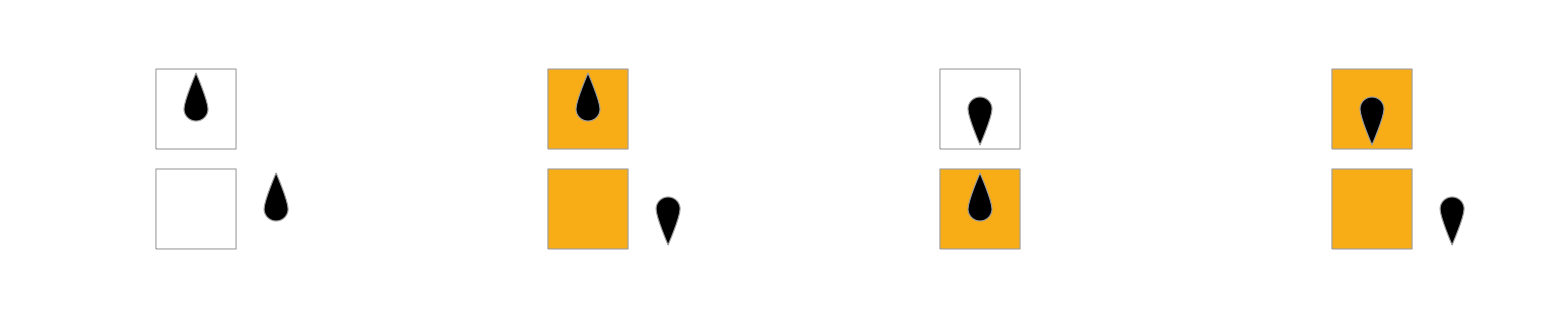

```mathematica
PlotMachine[program]
```

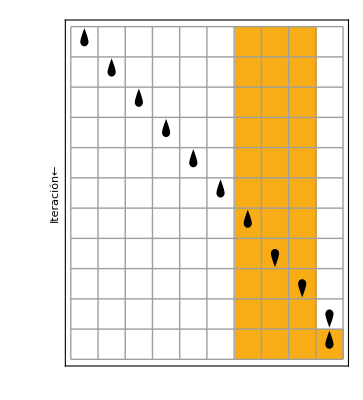

```mathematica
PlotExecution[program,-5,{{1,1,1},0}]
```

## Codificación de los argumentos

### Encoding

```mathematica
argCoding = {
0->{0},
1->{1,0},
","->{1,1,0}
};
CodifyArg[n_Integer]:=Flatten[IntegerDigits[n,2]/.argCoding];
CodifyArg[s_String]:= s/.argCoding;
CodifyArg[l_List]:=Flatten[Map[CodifyArg,Riffle[l,","]]];

ArgumentExpansion[l_List]:=CodifyArg[l];
ArgumentExpansion[n_]:=Flatten[Map[CodifyArg,{n,","}]];

TapeEncode[n_]:={ArgumentExpansion[n],0};
```

```mathematica
TapeEncode[167]
```

{{1,0,0,1,0,0,0,1,0,1,0,1,0,1,1,0},0}

### Decoding

```mathematica
argDecoding = {
{0}->0,
{1,0}->1,
{1,1,0}->","
};
Decode1Token[{}]:={Null,{}};
Decode1Token[l_]:=Block[{firstMatch},
firstMatch = First[SequenceCases[l,{0}|{1,0}|{1,1,0}]];
{firstMatch/.argDecoding,Drop[l,Length[firstMatch]]}
];
TapeDecodeToBinary[l_]:=DeleteCases[FixedPointList[Decode1Token[Last[#]]&,{Null,l}],{Null,_}][[All,1]];
TapeDecode[l_]:=Map[FromDigits[#,2]&,SequenceSplit[TapeDecodeToBinary[l],{","}]];
```

```mathematica
TapeDecode@{0,1,0,0,0,1,0,1,1,0,1,0,1,0,1,1,0,1,0,0,0,1,1,1,0,1,0,1,0,1,1,1,1,0,0,1,1,0}
```

{9,3,4,3,2}

```mathematica
TapeDecode@TapeEncode[167][[1]]
```

{167}

Ejemplo con XN+1

```mathematica
program = {
{0,0}->{0,0,1},
{0,1}->{1,1,1},
{1,0}->{0,0,1},
{1,1}->{2,1,1},
{2,0}->{3,0,-1},
{2,1}->{2,1,1},
{3,0}->{0,1,0},
{3,1}->{4,0,-1},
{4,0}->{5,1,-1},
{4,1}->{4,1,-1},
{5,0}->{6,0,1},
{5,1}->{2,1,1},
{6,1}->{7,1,1},
{7,0}->{3,1,1},
{7,1}->{7,0,1}
};
```

```mathematica
ProgramPrettify[program]
```

{0^0→0_R^0,1^0→1_R^1,0^1→0_R^0,1^1→1_R^2,0^2→0_L^3,1^2→1_R^2,0^3→1_H^0,1^3→0_L^4,0^4→1_L^5,1^4→1_L^4,0^5→0_R^6,1^5→1_R^2,1^6→1_R^7,0^7→1_R^3,1^7→0_R^7}

```mathematica
EncodeProgram[program]
```

450813704461563958982113775643437908

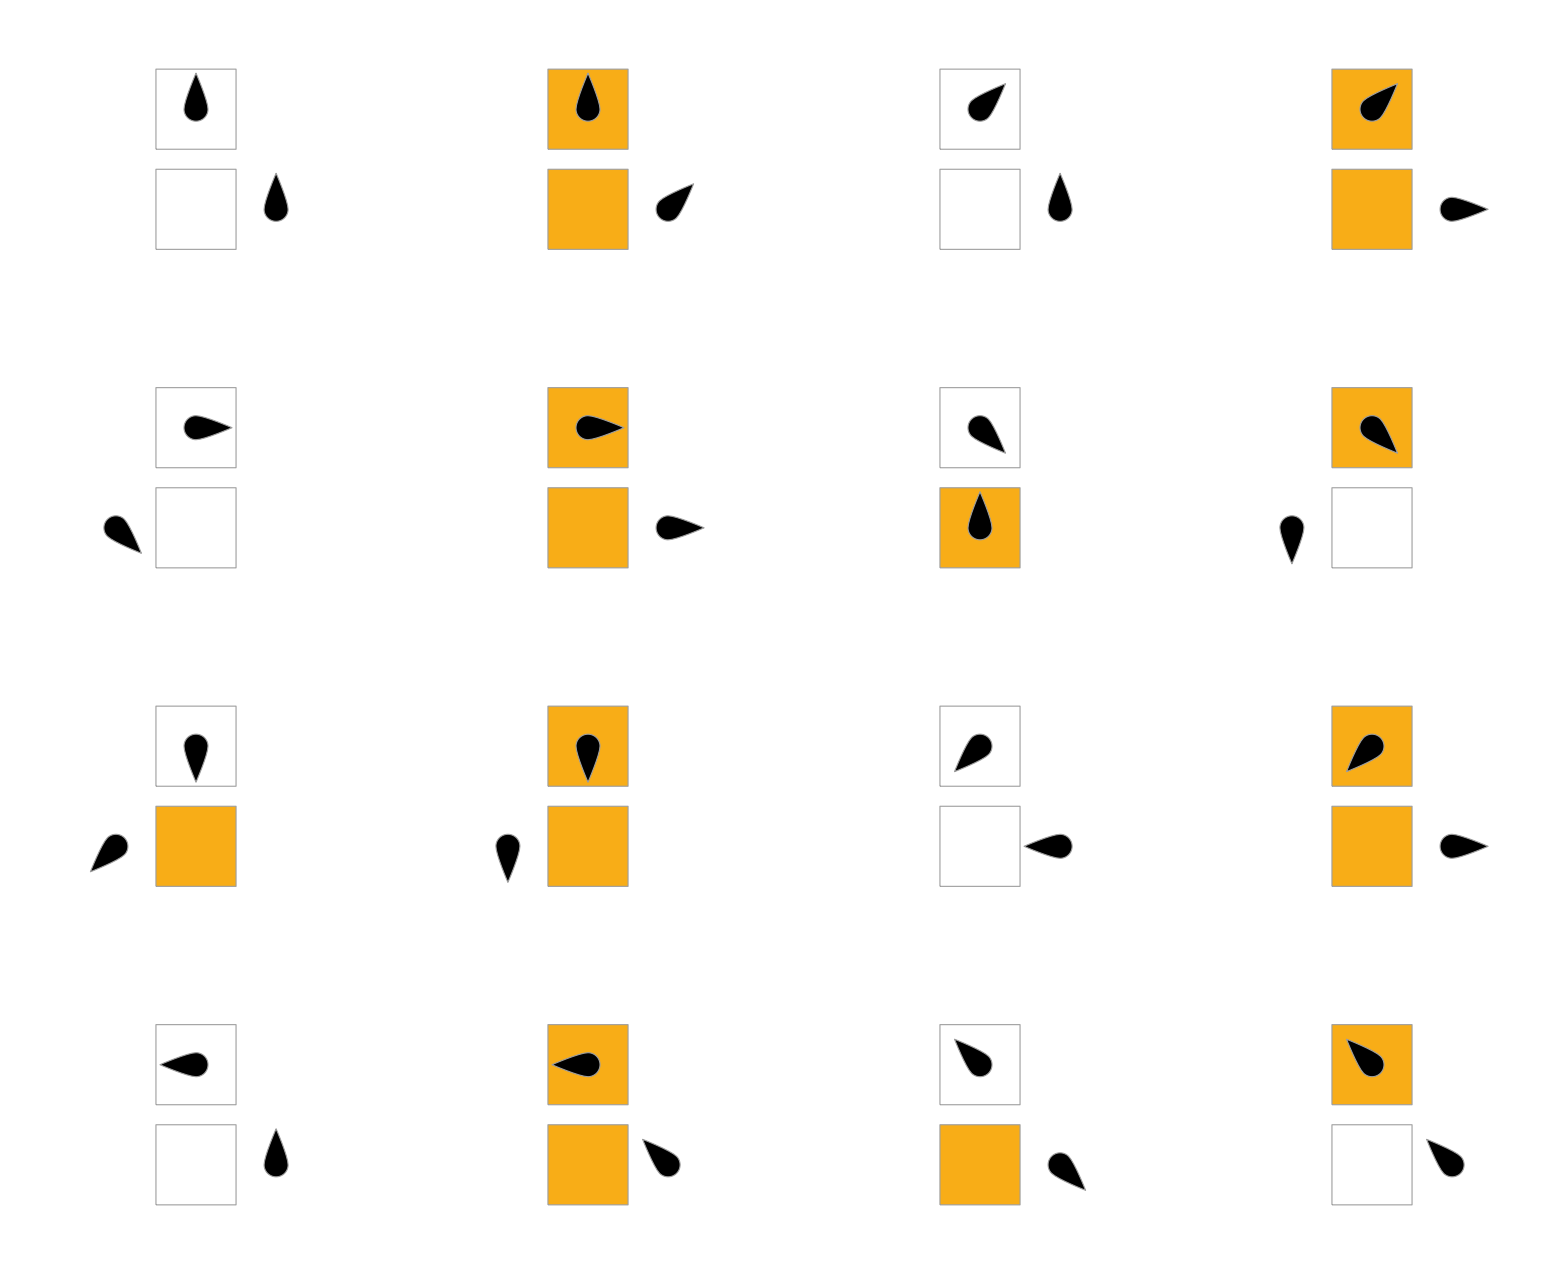

```mathematica
PlotMachine[program]
```

```mathematica
TapeDecode[MachineOutput[program,TapeEncode[167]]]
```

{168,0}

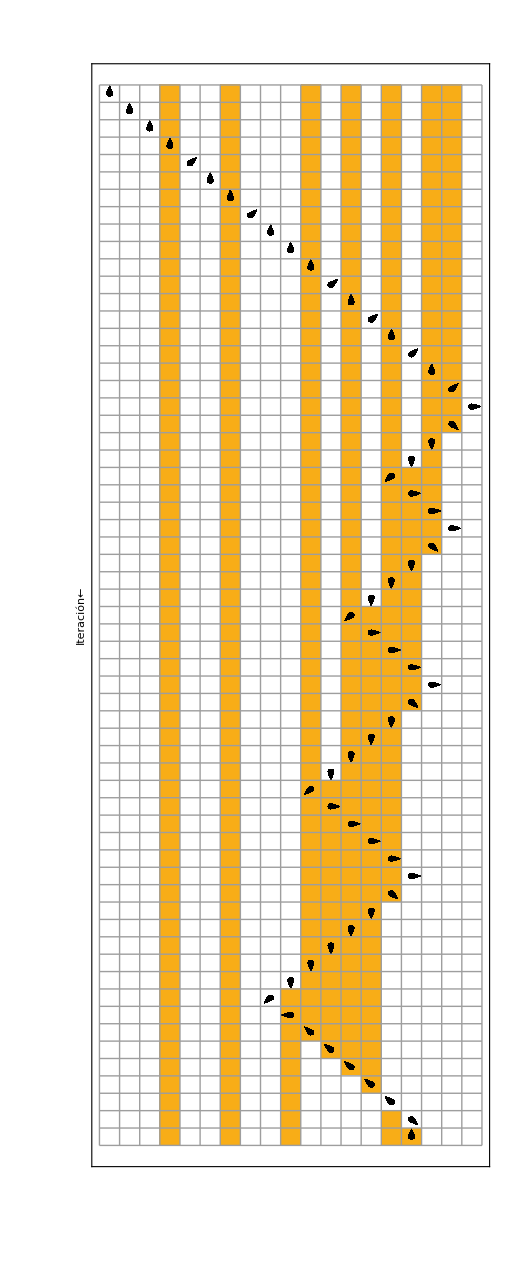

```mathematica
PlotExecution[program,-2,TapeEncode[167]]
```